```mathematica
Table[k->Style[Framed[k, FrameStyle->LightBlue],20,Red,Background->LightYellow],{k,1,3}]
```

{1→1,2→2,3→3}

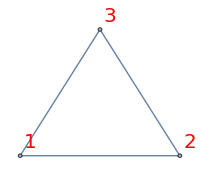

```mathematica
CompleteGraph[3,VertexLabels->Table[k->Style[Framed[k, FrameStyle->LightBlue],20,Red,Background->LightYellow],{k,1,3}], ImageSize->200]
```

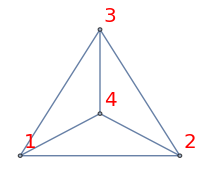

```mathematica
With[
{map=Association[1->4,2->2,3->3,4->1]},
CompleteGraph[4,VertexLabels->Table[k->Style[Framed[map[k], FrameStyle->LightBlue],20,Red,Background->LightYellow],{k,1,4}], ImageSize->200]
]
```

## Quadrilateral images

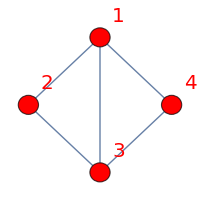

```mathematica
Graph[{1->2,2->3,3->4,4->1,1->3},VertexLabels->Table[k->Style[Framed[k, FrameStyle->LightBlue],20,Red,Background->LightYellow],{k,1,4}], ImageSize->200, DirectedEdges->False, GraphLayout->"TutteEmbedding", VertexStyle->Red, VertexSize->Medium]
```

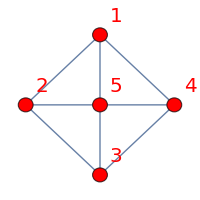

```mathematica
Graph[{1->2,2->3,3->4,4->1,1->5,2->5,3->5,4->5},VertexLabels->Table[k->Style[Framed[k, FrameStyle->LightBlue],20,Red,Background->LightYellow],{k,1,5}], ImageSize->200, DirectedEdges->False, GraphLayout->"TutteEmbedding", VertexStyle->Red, VertexSize->Medium]
```

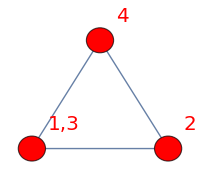

```mathematica
With[
{map=Association[1->"1,3",2->2,3->4]},Graph[{1->2,3->1,2->3},VertexLabels->Table[k->Style[Framed[map[k], FrameStyle->LightBlue],20,Red,Background->LightYellow],{k,1,3}], ImageSize->200, DirectedEdges->False,  VertexStyle->Red, VertexSize->Medium]
]
```

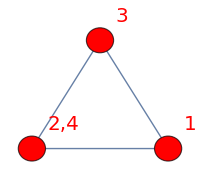

```mathematica
With[
{map=Association[1->"2,4",2->1,3->3]},Graph[{1->2,3->1,2->3},VertexLabels->Table[k->Style[Framed[map[k], FrameStyle->LightBlue],20,Red,Background->LightYellow],{k,1,3}], ImageSize->200, DirectedEdges->False,  VertexStyle->Red, VertexSize->Medium]
]
```

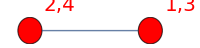

```mathematica
With[
{map=Association[1->"1,3",2->"2,4"]},Graph[{1->2},VertexLabels->Table[k->Style[Framed[map[k], FrameStyle->LightBlue],20,Red,Background->LightYellow],{k,1,2}], ImageSize->200, DirectedEdges->False,  VertexStyle->Red, VertexSize->Medium]
]
```

## The pentagon

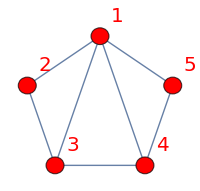

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{1->2,2->3,3->4,4->5,1->5,1->3,1->4},VertexLabels->Table[k->Style[Framed[k, FrameStyle->LightBlue],20,Red,Background->LightYellow],{k,1,5}], ImageSize->200, DirectedEdges->False, GraphLayout->"TutteEmbedding", VertexStyle->Red, VertexSize->Medium]
```

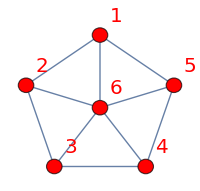

```mathematica
Graph[{1->2,2->3,3->4,4->5,1->5,1->6,2->6,3->6,4->6,5->6},VertexLabels->Table[k->Style[Framed[k, FrameStyle->LightBlue],20,Red,Background->LightYellow],{k,1,6}], ImageSize->200, DirectedEdges->False, GraphLayout->"TutteEmbedding", VertexStyle->Red, VertexSize->Medium]
```

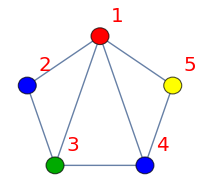

```mathematica
Graph[{1->2,2->3,3->4,4->5,1->5,1->3,1->4},VertexLabels->Table[k->Style[Framed[k, FrameStyle->LightBlue],20,Red,Background->LightYellow],{k,1,5}], ImageSize->200, DirectedEdges->False, GraphLayout->"TutteEmbedding", VertexStyle->{1->Red,2->Blue,3->Darker[Green],4->Blue,5->Yellow}, VertexSize->Medium]
```

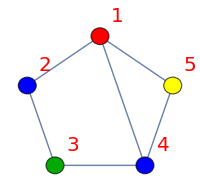

```mathematica
Graph[{1->2,2->3,3->4,4->5,1->5,1->4},VertexLabels->Table[k->Style[Framed[k, FrameStyle->LightBlue],20,Red,Background->LightYellow],{k,1,5}], ImageSize->200, DirectedEdges->False, GraphLayout->"TutteEmbedding", VertexStyle->{1->Red,2->Blue,3->Darker[Green],4->Blue,5->Yellow}, VertexSize->Medium]
```

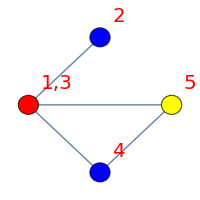

```mathematica
With[
{map=Association[1->"1,3",2->2,3->3,4->4,5->5]},
Graph[
VertexContract[Graph[{1->2,2->3,3->4,4->5,1->5,1->4}, ImageSize->200, DirectedEdges->False, GraphLayout->"TutteEmbedding"],{1,3}],
VertexLabels->Table[k->Style[Framed[map[k], FrameStyle->LightBlue],20,Red,Background->LightYellow],{k,1,5}],
VertexSize->Medium,
VertexStyle->{1->Red,2->Blue,3->Darker[Green],4->Blue,5->Yellow}
 ]
]
```

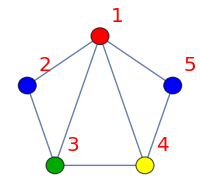

```mathematica
Graph[{1->2,2->3,3->4,4->5,1->5,1->3,1->4},VertexLabels->Table[k->Style[Framed[k, FrameStyle->LightBlue],20,Red,Background->LightYellow],{k,1,5}], ImageSize->200, DirectedEdges->False, GraphLayout->"TutteEmbedding", VertexStyle->{1->Red,2->Blue,3->Darker[Green],4->Yellow,5->Blue}, VertexSize->Medium]
```

## Lattices as pictures

```mathematica
pi4=EdgeList[MobiusGraph4[K4Key,allGraphs4]]
```

{n12x34->n1234,n13x24->n1234,n14x23->n1234,n123x4->n1234,n124x3->n1234,n134x2->n1234,n1x234->n1234,n12x3x4->n12x34,n1x2x34->n12x34,n13x2x4->n13x24,n1x24x3->n13x24,n14x2x3->n14x23,n1x23x4->n14x23,n12x3x4->n123x4,n13x2x4->n123x4,n1x23x4->n123x4,n12x3x4->n124x3,n14x2x3->n124x3,n1x24x3->n124x3,n13x2x4->n134x2,n14x2x3->n134x2,n1x2x34->n134x2,n1x23x4->n1x234,n1x24x3->n1x234,n1x2x34->n1x234,n1x2x3x4->n12x3x4,n1x2x3x4->n13x2x4,n1x2x3x4->n14x2x3,n1x2x3x4->n1x23x4,n1x2x3x4->n1x24x3,n1x2x3x4->n1x2x34}

```mathematica
SymbolToLabel3[s_]:=Row[Riffle[ StringSplit[StringDrop[SymbolName[s ],1],"x"],Style["|",Red,20]]]
```

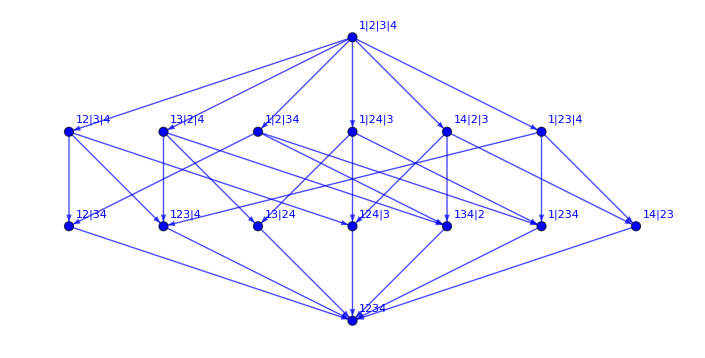

```mathematica
Graph[pi4,VertexLabels->Map[#->Framed[SymbolToLabel3[#]]&,VertexList[Graph[pi4]]],EdgeStyle->Blue,VertexStyle->Blue]
```

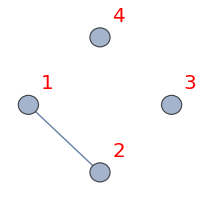

```mathematica
Graph[{1,2,3,4},{1->2},VertexLabels->Table[k->Style[Framed[k, FrameStyle->LightBlue],20,Red,Background->LightYellow],{k,1,4}], ImageSize->200, DirectedEdges->False, GraphLayout->"CircularEmbedding",  VertexSize->Medium]
```

```mathematica
Table[Labeled[allGraphs4[k,"graph"],k],{k,Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},EdgeCount[g]==1&&VertexCount[g]==4]&]}]
```

{-Graphics-243,-Graphics-81,-Graphics-27,-Graphics-9,-Graphics-3,-Graphics-1}

```mathematica
VertexList[MobiusGraph4[K4Key,allGraphs4]]
```

{n12x34,n13x24,n14x23,n1x2x3x4,n1234,n123x4,n124x3,n12x3x4,n134x2,n13x2x4,n14x2x3,n1x234,n1x23x4,n1x24x3,n1x2x34}

```mathematica
Descendants[MobiusGraph4[K4Key,allGraphs4],n12x3x4]
```

{n12x3x4,n12x34,n12x3x4->n12x34,n12x34,n1234,n12x34->n1234,n12x3x4,n123x4,n12x3x4->n123x4,n123x4,n1234,n123x4->n1234,n12x3x4,n124x3,n12x3x4->n124x3,n124x3,n1234,n124x3->n1234}

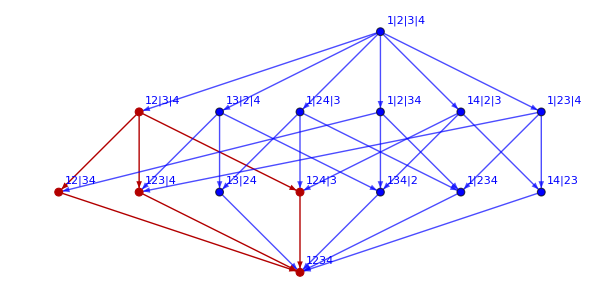

```mathematica
Graph[MobiusGraph4[K4Key,allGraphs4],GraphHighlight->Descendants[MobiusGraph4[K4Key,allGraphs4],n12x3x4],VertexLabels->Map[#->Framed[SymbolToLabel3[#]]&,VertexList[Graph[pi4]]],EdgeStyle->Blue,VertexStyle->Blue]
```

```mathematica
Table[Labeled[allGraphs4[k,"graph"],k],{k,Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},EdgeCount[g]==5&&VertexCount[g]==4]&]}]
```

{-Graphics-363,-Graphics-361,-Graphics-355,-Graphics-337,-Graphics-283,-Graphics-121}

```mathematica
Table[Labeled[allGraphs4[k,"graph"],k],{k,Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},EdgeCount[g]==4&&VertexCount[g]==4]&]}]
```

{-Graphics-360,-Graphics-354,-Graphics-352,-Graphics-336,-Graphics-334,-Graphics-328,-Graphics-282,-Graphics-280,-Graphics-274,-Graphics-256,-Graphics-120,-Graphics-118,-Graphics-112,-Graphics-94,-Graphics-40}

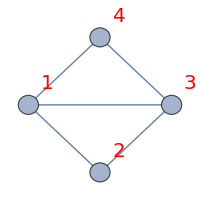

```mathematica
Graph[VertexList[allGraphs4[361,"graph"]],EdgeList[allGraphs4[361,"graph"]],VertexLabels->Table[k->Style[Framed[k, FrameStyle->LightBlue],20,Red,Background->LightYellow],{k,1,4}], ImageSize->200, DirectedEdges->False, GraphLayout->"CircularEmbedding",  VertexSize->Medium]
```

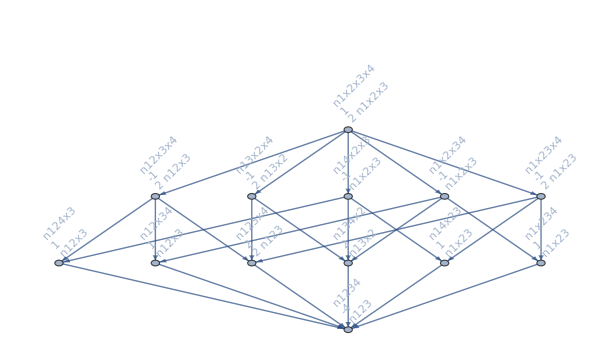

```mathematica
MobiusGraph4[361,allGraphs4]
```

```mathematica
DeleteDuplicates[Flatten[Table[Descendants[MobiusGraph4[K4Key,allGraphs4],v],{v,Select[VertexList[MobiusGraph4[361,allGraphs4]],StringCount[SymbolName[#],"x"]==2&]}]]]
```

{n12x3x4,n12x34,n12x3x4->n12x34,n1234,n12x34->n1234,n123x4,n12x3x4->n123x4,n123x4->n1234,n124x3,n12x3x4->n124x3,n124x3->n1234,n13x2x4,n13x24,n13x2x4->n13x24,n13x24->n1234,n13x2x4->n123x4,n134x2,n13x2x4->n134x2,n134x2->n1234,n14x2x3,n14x23,n14x2x3->n14x23,n14x23->n1234,n14x2x3->n124x3,n14x2x3->n134x2,n1x23x4,n1x23x4->n14x23,n1x23x4->n123x4,n1x234,n1x23x4->n1x234,n1x234->n1234,n1x2x34,n1x2x34->n12x34,n1x2x34->n134x2,n1x2x34->n1x234}

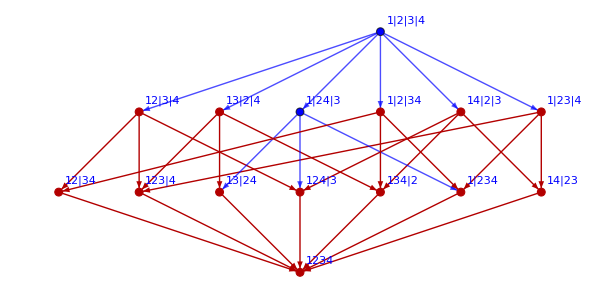

```mathematica
Graph[MobiusGraph4[K4Key,allGraphs4],GraphHighlight->DeleteDuplicates[Flatten[Table[Descendants[MobiusGraph4[K4Key,allGraphs4],v],{v,Select[VertexList[MobiusGraph4[361,allGraphs4]],StringCount[SymbolName[#],"x"]==2&]}]]],VertexLabels->Map[#->Framed[SymbolToLabel3[#]]&,VertexList[Graph[pi4]]],EdgeStyle->Blue,VertexStyle->Blue]
```

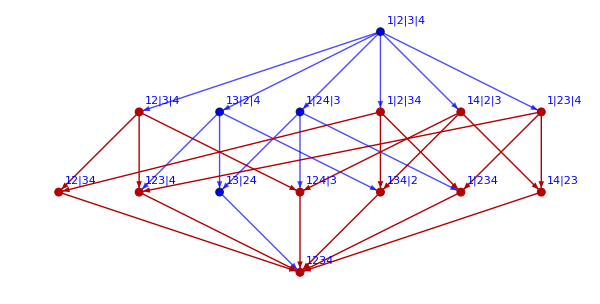

```mathematica
Graph[MobiusGraph4[K4Key,allGraphs4],GraphHighlight->DeleteDuplicates[Flatten[Table[Descendants[MobiusGraph4[K4Key,allGraphs4],v],{v,Select[VertexList[MobiusGraph4[280,allGraphs4]],StringCount[SymbolName[#],"x"]==2&]}]]],VertexLabels->Map[#->Framed[SymbolToLabel3[#]]&,VertexList[Graph[pi4]]],EdgeStyle->Blue,VertexStyle->Blue]
```

```mathematica
allGraphs4[280,"colofour"]
```

v13x24+v13x2x4+v1x24x3+v1x2x3x4

```mathematica
allGraphs4[361,"colofour"]
```

v1x24x3+v1x2x3x4

```mathematica
allGraphs4[442,"colofour"]
```

v13x24+v13x2x4

```mathematica
Table[Labeled[allGraphs4[k,"graph"],k],{k,Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},EdgeCount[g]==2&&VertexCount[g]==3]&]}]
```

{-Graphics-369,-Graphics-357,-Graphics-353,-Graphics-382,-Graphics-346,-Graphics-442,-Graphics-417,-Graphics-286,-Graphics-309,-Graphics-257,-Graphics-606,-Graphics-577,-Graphics-517,-Graphics-122,-Graphics-145,-Graphics-97,-Graphics-193,-Graphics-49}

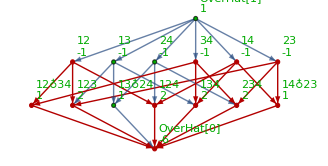
-Graphics-→-Graphics-

```mathematica
ShowDamage[allGraphs4,280]
```

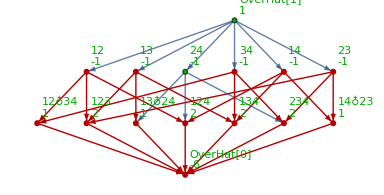
-Graphics-→-Graphics-

```mathematica
ShowDamage[allGraphs4,361]
```

```mathematica
ExamineGraph[allGraphs4[361,"graph"]]
```

{-Graphics-→{2,2,2,24 | OverHat[1] |  | },1<->2→{1,1,3,12 |  |  | },1<->3→{1,0,7/2,13 |  |  | },1<->4→{1,1,3,14 |  |  | },2<->3→{1,1,3,23 |  |  | },3<->4→{1,1,3,34 |  |  | }}

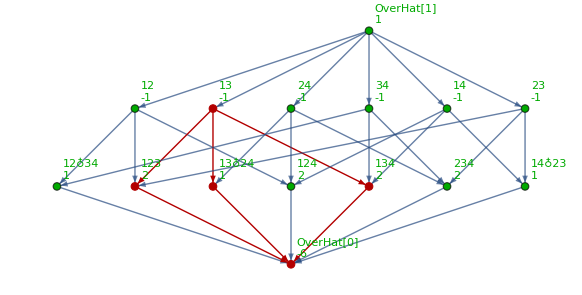
-Graphics-→-Graphics-

```mathematica
ShowDamage[allGraphs4,442]
```

```mathematica
MobiusGraph4[442,allGraphs4]
```

```mathematica
Map[SymbolToLabel2[#]&,ListofVars[allGraphs4[442,"colofourrealnull"]]]
```

{1234,13,123,134}

```mathematica
allGraphs4[442,"colofour"]
```

v13x24+v13x2x4